```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/temporary/Documents/Caltech_scripts/melting/Bernouli

```mathematica
ReadDataFromFile[st_String]:=Module[{fl,dataAll},fl=OpenRead[st];
dataAll=ReadList[fl,{Number,Number,Number,Number,Number,Number,Word,Number,Number}];
Close[fl];dataAll]
```

```mathematica
dataAll=Join[ReadDataFromFile["res.txt"],ReadDataFromFile["res_temp.txt"]];
```

```mathematica
(*dataAll={{5,1240,0,7},{5,1250,2,4},{5,1260,3,9},{5,1265,4,8},{5,1270,3,9},{5,1275,2,12},{5,1280,6,6},{5,1285,5,7},{5,1290,7,5},{5,1300,5,0},{5,1310,5,0},{6,1240,1,5},{6,1260,0,6},{6,1280,3,3},{6,1290,5,1},{6,1300,5,1},{6,1310,6,0},{6,1320,6,0},{6,1340,6,0}};*)
```

```mathematica
dataAll=ReadDataFromFile["Ge_1_1000.poss"];
```

```mathematica
Sizes=Union[Cases[dataAll,{_,_,_,n_,_,_,s_,_,t_}:>n]]
```

{5}

```mathematica
LogProb[r_,n_,res_]=(n-res) Log[1/(1+Exp[-r])]+res Log[1/(1+Exp[r])];
```

```mathematica
PriorTMin=950;
PriorTMax=970;
```

```mathematica
Res[n_]:=Module[{},dataList=Cases[dataAll,{_,_,_,n,_,_,s_,_,t_}:>{t,s}];
temps=Union[First/@dataList];
data=Table[{t,Count[dataList,{t,"liquid"}],Count[dataList,{t,"solid"}]},{t,temps}];
MyLogLikelihood[Tc_,α_]=Sum[LogProb[(d[[1]]-Tc) α,d[[2]]+d[[3]],d[[3]]],{d,data}];
s=FindMaximum[MyLogLikelihood[t,σ],{t,400,500},{σ,50,100}];
TMEAN=NIntegrate[t Exp[MyLogLikelihood[t,σ]-s[[1]]],{t,PriorTMin,PriorTMax},{σ,0,1},AccuracyGoal->5,MinRecursion->6]/NIntegrate[Exp[MyLogLikelihood[t,σ]-s[[1]]],{t,PriorTMin,PriorTMax},{σ,0,1},AccuracyGoal->5,MinRecursion->6];
TSIGMA=NIntegrate[(t-TMEAN)^2 Exp[MyLogLikelihood[t,σ]-s[[1]]],{t,PriorTMin,PriorTMax},{σ,0,1},AccuracyGoal->5,MinRecursion->6]/NIntegrate[Exp[MyLogLikelihood[t,σ]-s[[1]]],{t,PriorTMin,PriorTMax},{σ,0,1},AccuracyGoal->5,MinRecursion->6];
{n,TMEAN,2 Sqrt[TSIGMA]}]
```

```mathematica
ToPlot=Table[Res[n]
,{n,Sizes}]
```

{{5,955.598,1.01292}}

```mathematica
{{5,955.5979477701193}}
```

```mathematica
{{5,469.80026900822463,3.840908494951853}}
```

{{5,469.8,3.84091}}

```mathematica
Needs["ErrorBarPlots`"]
```

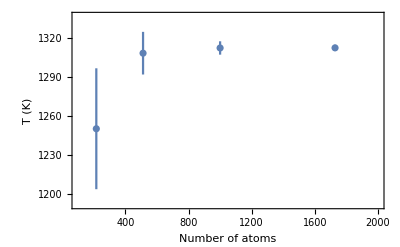

```mathematica
ErrorListPlot[Table[{{8 p[[1]]^3,p[[2]]},ErrorBar[p[[3]]]},{p,ToPlot}],PlotRange->{{100,2000},{1.1#[[1]]-0.1#[[2]],1.1#[[2]]-0.1#[[1]]}&@{Min@Table[p[[2]]-p[[3]],{p,ToPlot}],Max@Table[p[[2]]+p[[3]],{p,ToPlot}]}},Frame->True,FrameLabel->{"Number of atoms","T (K)"}]
```

```mathematica
Table[{i,4 i^3},{i,3,6}]
```

{{3,108},{4,256},{5,500},{6,864}}

```mathematica
Res[6]
```

{6,1312.28,2.34043}

```mathematica
Res[6]
```

{6,1312.8,2.42879}

```mathematica
data
```

{{1280,0,10},{1290,0,10},{1300,0,10},{1310,2,8},{1320,9,1},{1330,10,0}}

```mathematica
Round[i/.First@Solve[1.15^i==700/75,i]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

16

```mathematica
Table[4 i^3,{i,3,6}]
```

{108,256,500,864}

```mathematica
4 8^3
```

2048

```mathematica
{{474,473},{465,465},{363,362}}
```

{{474,473},{465,465},{363,362}}

```mathematica
1300+273-200+100 N@Table[(465-i)/(j-i),{i,{474,473}},{j,{363,362}}]
```

{{1381.11,1381.04},{1380.27,1380.21}}